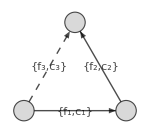

```mathematica
Graph[{s->m,m->p,s->p},EdgeWeight->{s->m->0.5,m->p->0.8,s->p->0.5*0.8},EdgeLabels->{s->m->{Subscript[f, 1],Subscript[c, 1]},m->p->{Subscript[f, 2],Subscript[c, 2]},s->p->{Subscript[f, 3],Subscript[c, 3]}},VertexLabels-> Placed[Automatic, Center], VertexSize->0.2, EdgeStyle->{Style,{Thick, Black},s->p->Dashed},
VertexStyle->LightGray,
ImageSize->150]
```

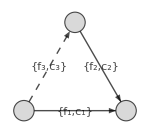

```mathematica
Graph[{s->m,p->m,s->p},EdgeWeight->{s->m->0.5,p->m->0.8,s->p->0.5*0.8},EdgeLabels->{s->m->{Subscript[f, 1],Subscript[c, 1]},p->m->{Subscript[f, 2],Subscript[c, 2]},s->p->{Subscript[f, 3],Subscript[c, 3]}},VertexLabels-> Placed[Automatic, Center], EdgeStyle->{Style,{Thick, Black},s->p->Dashed},
VertexStyle->LightGray,
VertexSize->0.2,ImageSize->150]
```

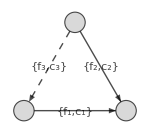

```mathematica
Graph[{s->m,p->m,p->s},EdgeWeight->{s->m->0.5,p->m->0.8,p->s->0.5*0.8},EdgeLabels->{s->m->{Subscript[f, 1],Subscript[c, 1]},p->m->{Subscript[f, 2],Subscript[c, 2]},p->s->{Subscript[f, 3],Subscript[c, 3]}},VertexLabels-> Placed[Automatic, Center], 
EdgeStyle->{Style,{Thick, Black},p->s->Dashed},
VertexStyle->LightGray,
 VertexSize->0.2, ImageSize->150]
```

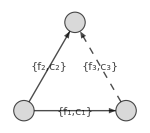

```mathematica
Graph[{m->s,m->p,s->p},EdgeWeight->{m->s->0.5,m->p->0.8,s->p->0.5*0.8},EdgeLabels->{m->s->{Subscript[f, 1],Subscript[c, 1]},m->p->{Subscript[f, 2],Subscript[c, 2]},s->p->{Subscript[f, 3],Subscript[c, 3]}},VertexLabels-> Placed[Automatic, Center], EdgeStyle->{Style,{Thick, Black},s->p->Dashed},
VertexStyle->LightGray, VertexSize->0.2, ImageSize->150]
```

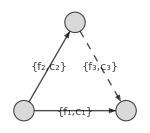

```mathematica
Graph[{m->s,m->p,p->s},EdgeWeight->{m->s->0.5,m->p->0.8,p->s->0.5*0.8},EdgeLabels->{m->s->{Subscript[f, 1],Subscript[c, 1]},m->p->{Subscript[f, 2],Subscript[c, 2]},p->s->{Subscript[f, 3],Subscript[c, 3]}},VertexLabels-> Placed[Automatic, Center], EdgeStyle->{Style,{Thick, Black},p->s->Dashed},
VertexStyle->LightGray,VertexSize->0.2,ImageSize->150]
```

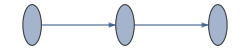

```mathematica
{Legended[Graph[{DirectedEdge[a,b],DirectedEdge[b,c]},VertexCoordinates->{a->{0,0}, b->{1,0}, c->{2,0}},VertexLabels-> Placed[Automatic, Center], VertexSize->0.2, EdgeStyle->{a->b->Green, b -> c->Green, {Thick}},ImageSize->250],LineLegend[{Directive[Thick, Green]},{"Predictive Link"}]]}
```

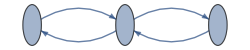

```mathematica
{Legended[Graph[{DirectedEdge[a,b],DirectedEdge[b,c],DirectedEdge[b,a],DirectedEdge[c,b]},VertexCoordinates->{a->{0,0}, b->{1,0}, c->{2,0}},VertexLabels-> Placed[Automatic, Center], VertexSize->0.2, EdgeStyle->{a->b->Green, b -> c->Green,b->a->Red,c->b->Red, {Thick}},
ImageSize->250],LineLegend[{Directive[Thick, Green],Directive[Thick, Red]},{"Predictive Link","Backward Conditioning"}]]}
```

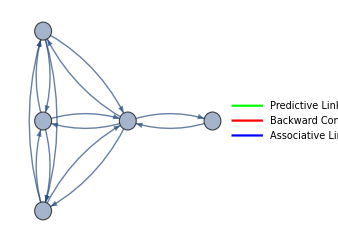

```mathematica
{Legended[Graph[{DirectedEdge[Subscript[a, 1],b], DirectedEdge[Subscript[a, 2],b],DirectedEdge[Subscript[a, 3],b],DirectedEdge[b,c],DirectedEdge[c,b],DirectedEdge[b,Subscript[a, 1]],DirectedEdge[b,Subscript[a, 2]],DirectedEdge[b,Subscript[a, 3]],DirectedEdge[Subscript[a, 1],Subscript[a, 2]], DirectedEdge[Subscript[a, 2],Subscript[a, 1]],DirectedEdge[Subscript[a, 2],Subscript[a, 3]], DirectedEdge[Subscript[a, 3],Subscript[a, 2]],DirectedEdge[Subscript[a, 1],Subscript[a, 3]], DirectedEdge[Subscript[a, 3],Subscript[a, 1]]},VertexCoordinates->{Subscript[a, 1]->{0,0}, Subscript[a, 2]->{0,1}, Subscript[a, 3]->{0,2}, b->{1,1},c->{2,1}},VertexLabels-> Placed[Automatic, Center], VertexSize->0.2,EdgeStyle->{Subscript[a, 1]->Subscript[a, 3]->Blue,Subscript[a, 3]->Subscript[a, 1]->Blue,Subscript[a, 1]->Subscript[a, 2]->Blue,Subscript[a, 2]->Subscript[a, 1]->Blue,Subscript[a, 2]->Subscript[a, 3]->Blue,Subscript[a, 3]->Subscript[a, 2]->Blue,Subscript[a, 1]->b->Green,Subscript[a, 2]->b->Green,Subscript[a, 3]->b->Green,b->Subscript[a, 1]->Red,b->Subscript[a, 2]->Red,b->Subscript[a, 3]->Red,b->c->Green,c->b->Red,{Thick}},ImageSize->250],LineLegend[{Directive[Thick, Green],Directive[Thick, Red],Directive[Thick, Blue]},{"Predictive Link","Backward Conditioning","Associative Link"}]]}
```

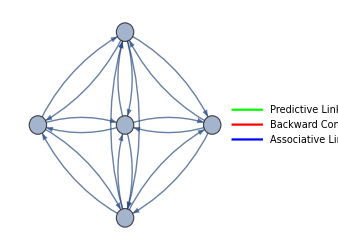

```mathematica
{Legended[Graph[{DirectedEdge[a,Subscript[b, 1]],DirectedEdge[a,Subscript[b, 2]],DirectedEdge[a,Subscript[b, 3]],DirectedEdge[Subscript[b, 1],c],DirectedEdge[Subscript[b, 2],c],DirectedEdge[Subscript[b, 3],c],DirectedEdge[c,Subscript[b, 1]],DirectedEdge[c,Subscript[b, 2]],DirectedEdge[c,Subscript[b, 3]],DirectedEdge[Subscript[b, 1],Subscript[b, 2]],DirectedEdge[Subscript[b, 2],Subscript[b, 3]],DirectedEdge[Subscript[b, 3],Subscript[b, 2]],
DirectedEdge[Subscript[b, 1],a],DirectedEdge[Subscript[b, 2],a],DirectedEdge[Subscript[b, 3],a],DirectedEdge[Subscript[b, 1],Subscript[b, 3]],DirectedEdge[Subscript[b, 2],Subscript[b, 1]],DirectedEdge[Subscript[b, 3],Subscript[b, 1]]},EdgeStyle->{Subscript[b, 1]->Subscript[b, 2]->Blue,Subscript[b, 2]->Subscript[b, 1]->Blue,Subscript[b, 2]->Subscript[b, 3]->Blue,Subscript[b, 3]->Subscript[b, 1]->Blue,Subscript[b, 1]->Subscript[b, 3]->Blue,Subscript[b, 3]->Subscript[b, 2]->Blue,a->Subscript[b, 1]->Green,a->Subscript[b, 2]->Green,a->Subscript[b, 3]->Green,Subscript[b, 1]->c->Green,c->Subscript[b, 1]->Red,Subscript[b, 2]->c->Green,c->Subscript[b, 2]->Red,Subscript[b, 3]->c->Green,c->Subscript[b, 3]->Red,
Subscript[b, 1]->a->Red,Subscript[b, 2]->a->Red,Subscript[b, 3]->a->Red,{Thick}}, VertexCoordinates->{Subscript[b, 1]->{1,0}, Subscript[b, 2]->{1,1}, Subscript[b, 3]->{1,2}, a->{0,1},c->{2,1}},VertexLabels-> Placed[Automatic, Center], VertexSize->0.2,ImageSize->250],LineLegend[{Directive[Thick, Green],Directive[Thick, Red],Directive[Thick, Blue]},{"Predictive Link","Backward Conditioning","Associative Link"}]]}
```

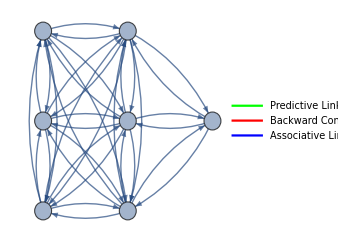

```mathematica
{Legended[Graph[{DirectedEdge[Subscript[a, 1],Subscript[b, 1]],DirectedEdge[Subscript[a, 1],Subscript[b, 2]],DirectedEdge[Subscript[a, 1],Subscript[b, 3]],
DirectedEdge[Subscript[a, 2],Subscript[b, 1]],DirectedEdge[Subscript[a, 2],Subscript[b, 2]],DirectedEdge[Subscript[a, 2],Subscript[b, 3]],
DirectedEdge[Subscript[a, 3],Subscript[b, 1]],DirectedEdge[Subscript[a, 3],Subscript[b, 2]],DirectedEdge[Subscript[a, 3],Subscript[b, 3]],
DirectedEdge[Subscript[b, 1],Subscript[a, 1]],DirectedEdge[Subscript[b, 1],Subscript[a, 2]],DirectedEdge[Subscript[b, 1],Subscript[a, 3]],DirectedEdge[Subscript[b, 2],Subscript[a, 1]],DirectedEdge[Subscript[b, 2],Subscript[a, 2]],DirectedEdge[Subscript[b, 2],Subscript[a, 3]],DirectedEdge[Subscript[b, 3],Subscript[a, 1]],DirectedEdge[Subscript[b, 3],Subscript[a, 2]],DirectedEdge[Subscript[b, 3],Subscript[a, 3]],
DirectedEdge[Subscript[a, 1],Subscript[a, 2]],DirectedEdge[Subscript[a, 2],Subscript[a, 1]],
DirectedEdge[Subscript[a, 2],Subscript[a, 3]],DirectedEdge[Subscript[a, 3],Subscript[a, 2]],
DirectedEdge[Subscript[a, 1],Subscript[a, 3]],DirectedEdge[Subscript[a, 3],Subscript[a, 1]],
DirectedEdge[Subscript[b, 1],c],DirectedEdge[Subscript[b, 2],c],DirectedEdge[Subscript[b, 3],c],
DirectedEdge[c,Subscript[b, 1]],DirectedEdge[c,Subscript[b, 2]],DirectedEdge[c,Subscript[b, 3]],
DirectedEdge[Subscript[b, 1],Subscript[b, 2]],DirectedEdge[Subscript[b, 2],Subscript[b, 3]],DirectedEdge[Subscript[b, 3],Subscript[b, 2]],DirectedEdge[Subscript[b, 1],Subscript[b, 3]],DirectedEdge[Subscript[b, 2],Subscript[b, 1]],DirectedEdge[Subscript[b, 3],Subscript[b, 1]]},
EdgeStyle->{Subscript[b, 1]->Subscript[b, 2]->Blue,Subscript[b, 2]->Subscript[b, 1]->Blue,Subscript[b, 2]->Subscript[b, 3]->Blue,Subscript[b, 3]->Subscript[b, 1]->Blue,Subscript[b, 1]->Subscript[b, 3]->Blue,Subscript[b, 3]->Subscript[b, 2]->Blue,
Subscript[a, 1]->Subscript[a, 2]->Blue,Subscript[a, 2]->Subscript[a, 1]->Blue,Subscript[a, 2]->Subscript[a, 3]->Blue,Subscript[a, 3]->Subscript[a, 1]->Blue,Subscript[a, 1]->Subscript[a, 3]->Blue,Subscript[a, 3]->Subscript[a, 2]->Blue,
Subscript[a, 1]->Subscript[b, 1]->Green,Subscript[a, 2]->Subscript[b, 1]->Green,Subscript[a, 3]->Subscript[b, 1]->Green,
Subscript[b, 1]->Subscript[a, 1]->Red,Subscript[b, 1]->Subscript[a, 2]->Red,Subscript[b, 1]->Subscript[a, 3]->Red,
Subscript[b, 2]->Subscript[a, 1]->Red,Subscript[b, 2]->Subscript[a, 2]->Red,Subscript[b, 2]->Subscript[a, 3]->Red,
Subscript[b, 3]->Subscript[a, 1]->Red,Subscript[b, 3]->Subscript[a, 2]->Red,Subscript[b, 3]->Subscript[a, 3]->Red,
Subscript[a, 1]->Subscript[b, 2]->Green,Subscript[a, 2]->Subscript[b, 2]->Green,Subscript[a, 3]->Subscript[b, 2]->Green,
Subscript[a, 1]->Subscript[b, 3]->Green,Subscript[a, 2]->Subscript[b, 3]->Green,Subscript[a, 3]->Subscript[b, 3]->Green,
Subscript[b, 1]->c->Green,c->Subscript[b, 1]->Red,Subscript[b, 2]->c->Green,c->Subscript[b, 2]->Red,Subscript[b, 3]->c->Green,c->Subscript[b, 3]->Red,{Thick}},  VertexCoordinates->{Subscript[b, 1]->{1,0}, Subscript[b, 2]->{1,1}, Subscript[b, 3]->{1,2}, Subscript[a, 1]->{0,0},Subscript[a, 2]->{0,1},Subscript[a, 3]->{0,2},c->{2,1}},VertexLabels-> Placed[Automatic, Center], VertexSize->0.2,ImageSize->250],LineLegend[{Directive[Thick, Green],Directive[Thick, Red],Directive[Thick, Blue]},{"Predictive Link","Backward Conditioning","Associative Link"}]]}
```